# Buck Converter

Switching L - (C || R) circuit between V=V during (0, ta) and V=0 (ground) during (ta, tc), where tc is cycle time
Equations :
  Inductor: Vi = L (d il)/dt
  Capacitor: ic = C (d vc)/dt
  Resistor: vr = R ir
  Current conservation: il = ic + ir
  Energy conservation: V = vl + vc and vc = vr

## Full Solution

```mathematica
DSolve[R il[t] + L il'[t] + R L CC il''[t]==V,il[t],t](*Inductor current*)
V-L D[il[t]/.%,t](*Capacitor voltage*)
```

{{il[t]→V/R+ⅇ^(1/2 (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) t) C[1]+ⅇ^(1/2 (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) t) C[2]}}

{V-L (1/2 ⅇ^(1/2 (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) t) (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) C[1]+1/2 ⅇ^(1/2 (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) t) (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) C[2])}

```mathematica
TimeCycle=10^-8;(*s*)
Setup={L->10^-6,CC->10^-6,R->10^4,V->50,ta->TimeCycle/2,tc->TimeCycle};(*H, F, Ohm, V, s, s*)
```

Below I stitch together the solutions for t<ta and t>ta. For t<ta I use the expressions above. For t>ta, I use the formulas above shifted in time by ta, i.e., il_(t>ta)[t] = il[t-ta], and V=0. The segment 0<t<ta is denoted by “A”, and the segment ta<t<tc by “B”. The coefficients are additionally denoted with “plus” or “minus” depending on the sign of the square root in the exponent. The explicit formulas for il and vc are given below in the plot.
The inductor current and capacitor voltage must be both continuous because otherwise their derivatives would contain Dirac’s deltas, which nature always solves with a BOOM.
Continuity and steady-state operation requires il_(t<ta)[t=ta]==il_(t>ta)[t=ta], il_(t<ta)[t=0]==il_(t>ta)[t=tc], vc_(t<ta)[t=ta]==vc_(t>ta)[t=ta] and vc_(t<ta)[t=0]==vc_(t>ta)[t=tc]

```mathematica
FullSol=NSolve[{V/R+ⅇ^(1/2 (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) ta) CAminus+ⅇ^(1/2 (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) ta) CAplus== CBminus+ CBplus,
ⅇ^(1/2 (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R))(tc-ta)) CBminus+ⅇ^(1/2 (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) (tc-ta)) CBplus==V/R+CAminus+CAplus,
V-L/2 ⅇ^(1/2 (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) ta) (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) CAminus-L/2 ⅇ^(1/2 (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) ta) (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) CAplus==-L/2  (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) CBminus-L/2  (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) CBplus,
-L/2 ⅇ^(1/2 (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R))(tc-ta)) (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) CBminus-L/2 ⅇ^(1/2 (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) (tc-ta)) (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) CBplus==V-L/2  (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) CAminus-L/2 (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) CAplus}/.Setup,{CAminus,CAplus,CBminus,CBplus}]//Simplify
```

{{CAminus→-0.0325001+12.5 ⅈ,CAplus→-0.0325001-12.5 ⅈ,CBminus→0.0325001-12.5 ⅈ,CBplus→0.0325001+12.5 ⅈ}}

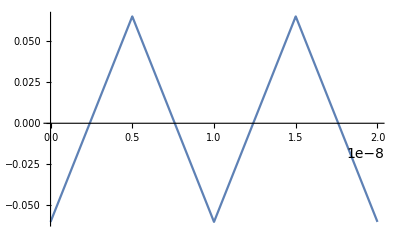

```mathematica
Plot[Re[Piecewise[Flatten[{{Re[V/R+ⅇ^(1/2 (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) FractionalPart[t/tc]tc) CAminus+ⅇ^(1/2 (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) FractionalPart[t/tc]tc) CAplus],0≤FractionalPart[t/tc]<ta/tc},{+ⅇ^(1/2 (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R))( FractionalPart[t/tc]tc-ta)) CBminus+ⅇ^(1/2 (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) (FractionalPart[t/tc]tc-ta)) CBplus,ta/tc≤FractionalPart[t/tc]<1}}/.FullSol/.Setup,1]]],{t,0,2 TimeCycle}](*Re[] just chops the imaginary part. Flatten[] is used to get rid of braces after the ReplaceAll is used. FractionalPart is used because I care only about the time modulo tc*)
```

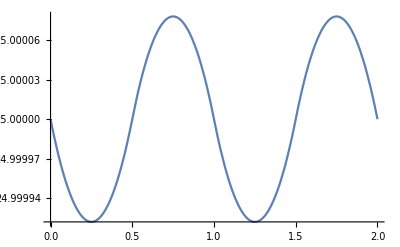

```mathematica
Plot[Re[Piecewise[Flatten[{{Re[V-L (1/2 ⅇ^(1/2 (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R))  FractionalPart[t/tc]tc) (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) CAminus+1/2 ⅇ^(1/2 (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R))  FractionalPart[t/tc]tc) (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) CAplus)],0≤FractionalPart[t/tc]<ta/tc},{-L (1/2 ⅇ^(1/2 (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) (FractionalPart[t/tc]tc-ta)) (-1/(CC R)-(√(L-4 CC R^2))/(CC √L R)) CBminus+1/2 ⅇ^(1/2 (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) (FractionalPart[t/tc]tc-ta)) (-1/(CC R)+(√(L-4 CC R^2))/(CC √L R)) CBplus),ta/tc≤FractionalPart[t/tc]<1}}/.FullSol/.Setup,1]]],{t,0,2 TimeCycle}]
```

The current plot seems to match very well the LTSpice simulation (note that the simulation takes the inductor current in the opposite direction as what I have done here, because it is more intuitive so), while the voltage is oscillating exactly around what we expect

## Second Order Approximation

Use Ansatz il[t]=i0 + m t + q t^2
Continuity is already built-in in this formula
il_(t<ta)[t] = i0 + ma t + qa t^2
il_(t<tc)[t] = il_(t<ta)[ta] + mb (t-ta) + qb (t-ta)^2
We have 5 variables: i0, ma, mb, qa and qb. We will see that we have 5 equations to solve for them

First, the quadratic coefficients are determined by substituting each part of the piecewise function into the differential equation for il[t] and comparing the 0th-order terms.

```mathematica
QuadTerms=Solve[{V/R ==i0 + L ma/R+L CC 2 qa,
0==i0+ma ta-mb ta+qa ta^2+qb ta^2+L/R(mb-2qb ta)+L CC 2qb
},{qa,qb}]//Simplify
```

{{qa→-(L ma+i0 R-V)/(2 CC L R),qb→(-2 CC L (L mb+R (i0+ma ta-mb ta))+ta^2 (L ma+i0 R-V))/(2 CC L (2 CC L R+ta (-2 L+R ta)))}}

Second, steady - state operation il[tc] = il[t = 0] and vc[tc] = vc[t = 0] is enforced, as well as continuity in vc[ta]

```mathematica
QuadSol=Solve[{ma ta+mb(tc-ta)+qa ta^2+qb(tc-ta)^2==0,
V-L(ma+2qa ta)==-L mb,
-L mb-2L qb(tc-ta)==V-L ma,
V≠0,ta≠0,tc≠0,L≠0,ta≠tc,i0≠0,R≠0,L≠0,CC≠0}/.QuadTerms//Flatten,{ma,mb,i0}]//Simplify
```

{{ma→-(2 (CC R-ta) (ta-tc) V)/((2 CC L R+ta (-2 L+R ta)) tc),mb→(ta (-2 CC L R+2 L ta+R ta (-2 ta+tc)) V)/(L (2 CC L R+ta (-2 L+R ta)) tc),i0→(ta (-2 L ta+2 CC R (L+R (ta-tc))+R ta tc) V)/(R (2 CC L R+ta (-2 L+R ta)) tc)}}

```mathematica
IL=Piecewise[{{i0+ma FractionalPart[t/tc]tc+qa (FractionalPart[t/tc]tc)^2,0≤FractionalPart[t/tc]<ta/tc},{i0+ma ta+mb(FractionalPart[t/tc]tc-ta)+qa ta^2+qb(FractionalPart[t/tc]tc-ta)^2,ta/tc≤FractionalPart[t/tc]<1}}];
VC=Piecewise[{{V-L(ma +2qa FractionalPart[t/tc]tc),0≤FractionalPart[t/tc]<ta/tc},{-L(mb+2qb (FractionalPart[t/tc]tc-ta)),ta/tc≤FractionalPart[t/tc]<1}}];
```

```mathematica
TimeCycle=10^-8;(*s*)
Setup={L->10^-6,CC->10^-6,R->10^4,V->50,ta->TimeCycle/2,tc->TimeCycle};(*H, F, Ohm, V, s, s*)
```

```mathematica
QuadTerms/.QuadSol/.Setup//N
QuadSol/.QuadTerms/.Setup//N
```

{{{qa→6.24993×10^10,qb→-6.24993×10^10}}}

{{{ma→2.49997×10^7,mb→-2.49997×10^7,i0→-0.122498}}}

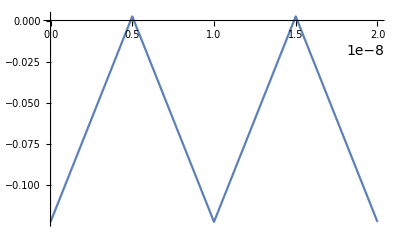

```mathematica
Plot[IL/.QuadTerms/.QuadSol/.Setup,{t,0,2 TimeCycle}]
```

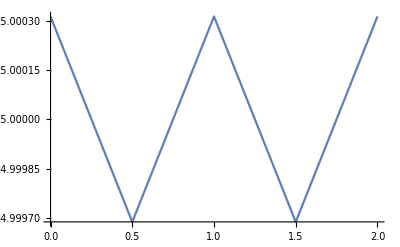

```mathematica
Plot[VC/.QuadTerms/.QuadSol/.Setup,{t,0,2 TimeCycle}]
```

## Linear Approximation

For comparison with the quadratic solution
The differential equation is helpless here, because it is second order, while this approximation is just linear. In general, to approximate a nth-order differential equation you require a nth-order polynomial.
So, we have three variables: i0, ma and mb. We need three equations for them (continuity at il[ta] is again built-in).
The three equations could be continuity in vc[ta] and steady-state in il[tc] and vc[tc], but there is a problem. In this linear approximation, vc[t] is a constant, meaning that the equations for continuity and steady-state are the same. Moreover, i0 does not feature in any of these equations. So we have to come up with a third independent equation to solve for i0. This is achieved in the lecture notes by setting to 0 the charge acquired by the capacitor during one cycle. So, the third equation is Integrate[ic[t], {t,0,tc}] = 0, which I expanded by hand.

```mathematica
LinSol=Solve[{ma ta+mb(tc-ta)==0,
V-L ma==-L mb,
i0 tc+ma ta tc-ma/2 ta^2+mb/2(tc^2-ta^2)+V/R tc==0,
V≠0,ta≠0,tc≠0,L≠0,ta≠tc,R≠0,L≠0,CC≠0}//Flatten,{ma,mb,i0}]//Simplify
```

{{ma→((-ta+tc) V)/(L tc),mb→-(ta V)/(L tc),i0→-V/R-(ta (2 ta^2-3 ta tc+tc^2) V)/(2 L tc^2)}}

```mathematica
ILlin=Piecewise[{{i0+ma FractionalPart[t/tc]tc,0≤FractionalPart[t/tc]<ta/tc},{i0+ma ta+mb(FractionalPart[t/tc]tc-ta),ta/tc≤FractionalPart[t/tc]<1}}];
VClin=Piecewise[{{V-L ma,0≤FractionalPart[t/tc]<ta/tc},{-L mb,ta/tc≤FractionalPart[t/tc]<1}}];
```

```mathematica
TimeCycle=10^-8;(*s*)
Setup={L->10^-6,CC->10^-6,R->10^4,V->50,ta->TimeCycle/2,tc->TimeCycle};(*H, F, Ohm, V, s, s*)
```

```mathematica
LinSol/.Setup//N
```

{{ma→2.5×10^7,mb→-2.5×10^7,i0→-0.005}}

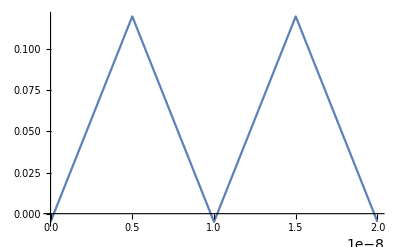

```mathematica
Plot[ILlin/.LinSol/.Setup,{t,0,2 TimeCycle}]
```

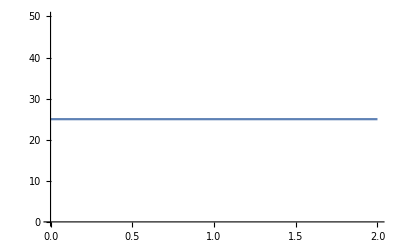

```mathematica
Plot[VClin/.LinSol/.Setup,{t,0,2 TimeCycle}]
```